```mathematica
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.49941;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;d2=0.0;

s=NDSolve[{T'[x]==(0.244597*T[x])/((1+(T[x]/1088.66)^μ)^(1/μ)),S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-ϵ*T[x]/(1+T[x]/m2))* S[x]-(d+((d2*T[x])/(1+(T[x]/m2))))*M[x],T[0]==6.86,S[0]==252.5,M[0]==4797.08},{T,S,M},{x,0,5000}];
pl1=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,0,5000}, PlotStyle->Red,(*PlotLegends->Placed[{"C26"},Above],*)(*PlotLegends->Placed[{"C26"},{0.1,0.47}]*)PlotLegends->Placed[{"C26"},{0.85,0.85}],PlotRange->{{0,400},{0,800}}];
(*************************************)

P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0;A2=0.89;A3=0.4;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[5]==22.68,S[5]==184.98,M[5]==4691.31},{T,S,M},{x,5,5000}];
pl2=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,5,5000},PlotRange->All, PlotStyle->Darker[Blue](*PlotRange->{{0,50},{0,1}},*),PlotLegends->Placed[{"Day 5^th"},{0.85,0.75}]];

P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))* S[x]-d*M[x],T[0]==6.86,S[0]==249.8,M[0]==4746.44},{T,S,M},{x,0,5000}];
pl3=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,0,5},PlotRange->All, PlotStyle->Darker[Blue]];
(*************************************)
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0;A2=0.89;A3=0.4;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[9]==59.03,S[9]==144.27,M[9]==4474.2},{T,S,M},{x,9,5000}];
pl6=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,9,5000},PlotRange->All, PlotStyle->Darker[Green](*PlotRange->{{0,50},{0,1}},*),PlotLegends->Placed[{"Day 9^th"},{0.65,0.75}]];

P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))* S[x]-d*M[x],T[0]==6.86,S[0]==249.8,M[0]==4746.44},{T,S,M},{x,0,5000}];
pl7=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,0,9},PlotRange->All,PlotStyle->Darker[Green]];
(*************************************)
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0;A2=0.89;A3=0.4;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[14]==195.13,S[14]==106.9,M[14]==4099.5},{T,S,M},{x,14,5000}];
pl10=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,14,5000},PlotRange->All,PlotStyle->Darker[Purple](*PlotRange->{{0,50},{0,1}},*),PlotLegends->Placed[{"Day 5^th"},{0.85,0.65}]];

P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))* S[x]-d*M[x],T[0]==6.86,S[0]==249.8,M[0]==4746.44},{T,S,M},{x,0,5000}];
pl11=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,0,14},PlotRange->All,PlotStyle->Darker[Purple]];
(*************************************)
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0;A2=0.89;A3=0.4;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[16]==314.73,S[16]==95.44,M[16]==3935.698},{T,S,M},{x,16,5000}];
pl12=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,16,5000},PlotRange->All, PlotStyle->Darker[Orange](*PlotRange->{{0,50},{0,1}},*),PlotLegends->Placed[{"Day 16^th"},{0.65,0.65}]];

P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))* S[x]-d*M[x],T[0]==6.86,S[0]==249.8,M[0]==4746.44},{T,S,M},{x,0,5000}];
pl13=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,0,16},PlotRange->All, PlotStyle->Darker[Orange]];
(*************************************)
P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;A1=0;A2=0.89;A3=0.4;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))*S[x]-A2*((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-A1*(ϵ*T[x]/(1+T[x]/m2)))* S[x]-A3*d*M[x],T[21]==1000.043,S[21]==73.63,M[21]==3523.1},{T,S,M},{x,21,5000}];
pl16=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,21,5000},PlotRange->All, PlotStyle->Darker[Yellow](*PlotRange->{{0,50},{0,1}},*),PlotLegends->Placed[{"Day 21^st"},{0.85,0.55}]];

P0=0.479;P1=0.133;v0=0.087;v1=5.591;μ=4.560124;m=1000;d=0.05;m2=1.001;ϵ=0.01;d1=0.07;
s=NDSolve[{T'[x]-(0.239141*T[x])/((1+(T[x]/1008.25)^μ)^(1/μ))==0,S'[x]==(2 *(P0+P1/(1+M[x]/m))-1)* (v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))*S[x]-((d1*T[x])/(1+(T[x]/m2)))*S[x],M'[x]==2 *(1-P0-P1/(1+M[x]/m))*(v0+v1/(1+M[x]/m)-(ϵ*T[x]/(1+T[x]/m2)))* S[x]-d*M[x],T[0]==6.86,S[0]==249.8,M[0]==4746.44},{T,S,M},{x,0,5000}];
pl17=Plot[(M[x]/.s)/(S[x]/.s)(*(0.002*S[x]/.s)*),{x,0,21},PlotRange->All,  PlotStyle->Darker[Yellow]];
(*++++++++++++++++++++++++++++++++++++++++++++++++++++*)
```

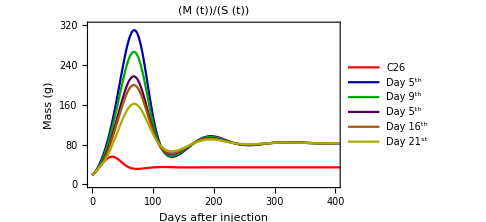

```mathematica
ppl1=Show[pl1,pl2,pl3,pl6,pl7,pl10,pl11,pl12,pl13,pl16,pl17,PlotRange->{{0,400},{0,320}},ImageSize->Medium,Frame->True,ImageSize->Medium,Frame->True,FrameLabel->{"Days after injection","Mass (g)"},FrameStyle->Directive[Black,12],PlotLabel->"(M (t))/(S (t))",LabelStyle->Directive[(*Bold,*)Black,13]]
```

```mathematica
Export["D:/sup2.eps",ppl1]
```

D:/sup2.eps